# Project 2 : Rigid - body dynamics

## TASK 1

```mathematica
I1=0.8;I2=0.9;I3=1.0;
w1[0]=1.;w2[0]=0.;w3[0]=2.;
```

```mathematica
EE=(I1*w1[0]^2 + I2*w2[0]^2 + I3*w3[0]^2)/2 ;
M= Sqrt[(I1*w1[0])^2 + (I2*w2[0])^2 + (I3*w3[0])^2];
```

```mathematica
τ[t_] :=t*Sqrt[(I3-I2)*(M^2-2*EE*I1)/(I1*I2*I3)]
k=Sqrt[(I2-I1)*(2*EE*I3-M^2)/((I3-I2)*(M^2-2*EE*I1))];
```

```mathematica
w1[t_]:=Sqrt[(2*EE*I3-M^2)/(I1*(I3-I1))]*JacobiCN[τ[t],k^2]
w2[t_]:=Sqrt[(2*EE*I3-M^2)/(I2*(I3-I2))]*JacobiSN[τ[t],k^2]
w3[t_]:=Sqrt[(M^2-2*EE*I1)/(I3*(I3-I1))]*
JacobiDN[τ[t],1*k^2]
```

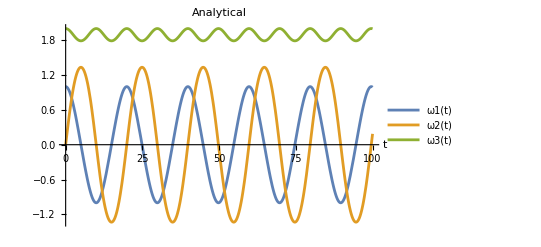

```mathematica
Plot[{w1[t],w2[t],w3[t]},{t,0,100},PlotLabel->"Analytical",AxesLabel->{"t"},PlotLegends->{"ω1(t)","ω2(t)","ω3(t)"}]
```

```mathematica
Ea[t_]:=(I1*w1[t]^2+I2*w2[t]^2+I3*w3[t]^2)/2
```

```mathematica
are [t_]:=Log[Abs[(Ea[t]-Ea[0])/Ea[0]] ]
```

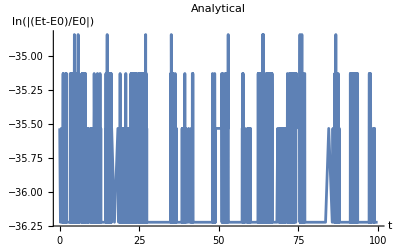

```mathematica
Plot[are [t],{t,0,100},PlotLabel->"Analytical",AxesLabel->{"t","ln(|(Et-E0)/E0|)"}]
```

## TASK 2

```mathematica
dt=0.1;
```

```mathematica
I231=(I2-I3)/I1;
I312=(I3-I1)/I2;
I123=(I1-I2)/I3;
```

```mathematica
f[w2_,w3_]:=I231*w2*w3;
g[w1_,w3_]:=I312*w3*w1;
h[w1_,w2_]:=I123*w1*w2;
```

```mathematica
dw1={{0,w1[0]}};
dw2={{0,w2[0]}};
dw3={{0,w3[0]}};
t=Array[# &,Ceiling[100/dt]+1,{0,100}];

For[i=1,i<=Ceiling[100/dt],i++,
k1=f[dw2[[i,2]],dw3[[i,2]]];
l1=g[dw1[[i,2]],dw3[[i,2]]];
m1=h[dw1[[i,2]],dw2[[i,2]]];

k2=f[dw2[[i,2]]+dt*l1/2,dw3[[i,2]]+dt*m1/2];
l2=g[dw1[[i,2]]+dt*k1/2,dw3[[i,2]]+dt*m1/2];
m2=h[dw1[[i,2]]+dt*k1/2,dw2[[i,2]]+dt*l1/2];

k3=f[dw2[[i,2]]+dt*l2/2,dw3[[i,2]]+dt*m2/2];
l3=g[dw1[[i,2]]+dt*k2/2,dw3[[i,2]]+dt*m2/2];
m3=h[dw1[[i,2]]+dt*k2/2,dw2[[i,2]]+dt*l2/2];

k4=f[dw2[[i,2]]+dt*l3,dw3[[i,2]]+dt*m3];
l4=g[dw1[[i,2]]+dt*k3,dw3[[i,2]]+dt*m3];
m4=h[dw1[[i,2]]+dt*k3,dw2[[i,2]]+dt*l3];

ww1 = dw1[[i,2]]+(dt/6)*(k1+2*k2+2*k3+k4);
ww2 = dw2[[i,2]]+(dt/6)*(l1+2*l2+2*l3+l4);
ww3 = dw3[[i,2]]+(dt/6)*(m1+2*m2+2*m3+m4);

AppendTo[dw1,{t[[i+1]],ww1}];
AppendTo[dw2,{t[[i+1]],ww2}];
AppendTo[dw3,{t[[i+1]],ww3}];]
```

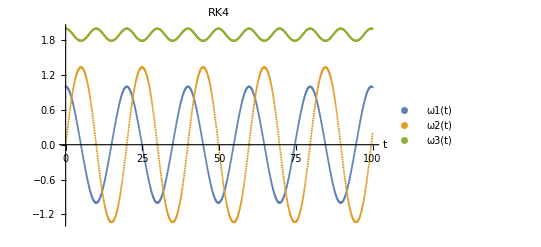

```mathematica
ListPlot[{dw1,dw2,dw3},PlotLabel->"RK4",AxesLabel->{"t"},PlotLegends->{"ω1(t)","ω2(t)","ω3(t)"}]
```

```mathematica
En=(I1*dw1[[All, 2]]^2 + I2*dw2[[All, 2]]^2 + I3*dw3[[All, 2]]^2)/2;
nre=Transpose[{t, Log[Abs[(En-En[[1]])/En[[1]]]]}];
```

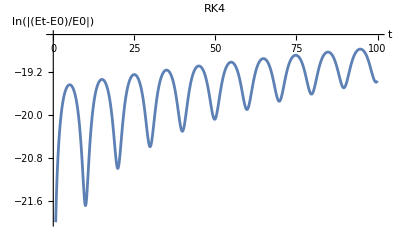

```mathematica
ListLinePlot[nre, PlotRange->{-22,-18.5},PlotLabel->"RK4",AxesLabel->{"t","ln(|(Et-E0)/E0|)"}]
```

## TASK 3

```mathematica
dt2=0.02;
MM={I1*w1[0],I2*w2[0],I3*w3[0]};
```

```mathematica
Rx[t_]:=RotationMatrix[t,{1,0,0}]
Ry[t_]:=RotationMatrix[t,{0,1,0}]
Rz[t_]:=RotationMatrix[t,{0,0,1}]
```

```mathematica
ΦHM1[t_,M_]:=Rx[M[[1]]*t/I1].M;
ΦHM2[t_,M_]:=Ry[M[[2]]*t/I2].M;
ΦHM3[t_,M_]:=Rz[M[[3]]*t/I3].M;
```

```mathematica
d2w1={{0,w1[0]}};
d2w2={{0,w2[0]}};
d2w3={{0,w3[0]}};
t2=Array[# &,Ceiling[100/dt2]+1,{0,100}];

For[i=1,i<=Ceiling[100/dt2],i++,
MM=ΦHM1[dt2/2,MM];
MM=ΦHM2[dt2/2,MM];
MM=ΦHM3[dt2,MM];
MM=ΦHM2[dt2/2,MM];
MM=ΦHM1[dt2/2,MM];

AppendTo[d2w1,{t2[[i]],MM[[1]]/I1}];
AppendTo[d2w2,{t2[[i]],MM[[2]]/I2}];
AppendTo[d2w3,{t2[[i]],MM[[3]]/I3}];]
```

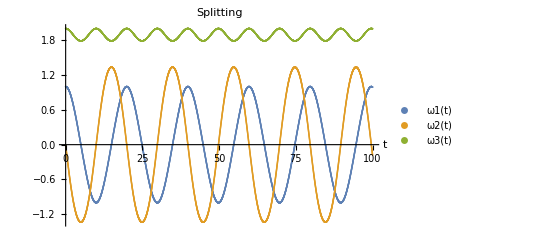

```mathematica
ListPlot[{d2w1,d2w2,d2w3},PlotLabel->"Splitting",AxesLabel->{"t"},PlotLegends->{"ω1(t)","ω2(t)","ω3(t)"}]
```

```mathematica
En2=(I1*d2w1[[All, 2]]^2 + I2*d2w2[[All, 2]]^2 + I3*d2w3[[All, 2]]^2)/2;
n2re=Transpose[{t2, Log[Abs[(En2-En2[[1]])/En2[[1]]]]}];
```

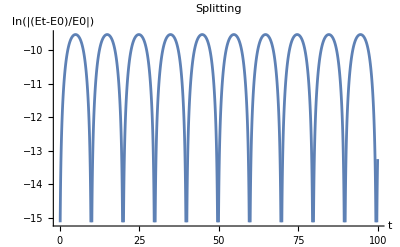

```mathematica
ListLinePlot[n2re,PlotLabel->"Splitting",AxesLabel->{"t","ln(|(Et-E0)/E0|)"}]
```